```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/c++/seminar"];
```

```mathematica
Oscillator=Import["oscillator.dat"];
```

```mathematica
xList=Oscillator.{{1,0},{0,1},{0,0}};
```

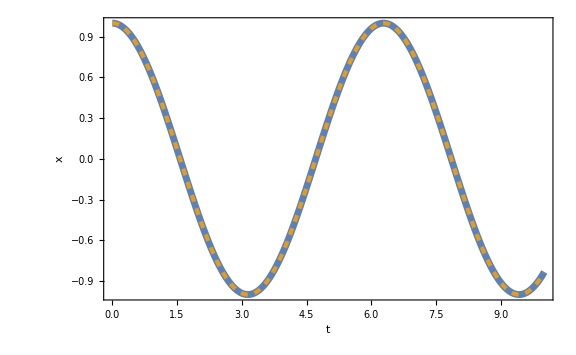

```mathematica
Show[ListPlot[xList,FrameLabel->{t,x},PlotLegends->Placed[LineLegend[{"num"},LegendMarkerSize->30],{0.87,0.8}],PlotStyle->AbsoluteThickness[5]],Plot[Cos[t],{t,0,10},PlotStyle->{Color[2],Dashed,AbsoluteThickness[3]},PlotLegends->Placed[LineLegend[{"cos t"},LegendMarkerSize->30],{0.87,0.8}]]]
```

```mathematica
Osc2=Import["2oscillator.dat"];
```

```mathematica
xList=Osc2.{{1,0},{0,1},{0,0},{0,0},{0,0}};
yList=Osc2.{{1,0},{0,0},{0,0},{0,1},{0,0}};
```

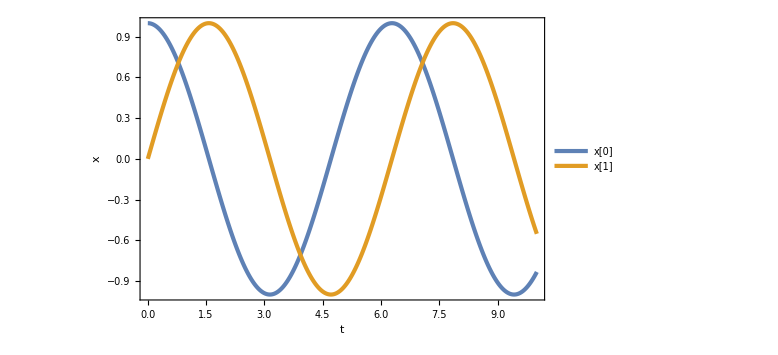

```mathematica
ListPlot[{xList,yList},FrameLabel->{t,x},PlotLegends->Placed[{"x[0]","x[1]"},{0.1,0.2}]]
```